```mathematica
Clear[k,r,a,b]
Get["toy2D`"];
```

k::shdw: Symbol k appears in multiple contexts {toy2D`,cephalon`}; definitions in context toy2D` may shadow or be shadowed by other definitions.

r::shdw: Symbol r appears in multiple contexts {toy2D`,cephalon`}; definitions in context toy2D` may shadow or be shadowed by other definitions.

a::shdw: Symbol a appears in multiple contexts {toy2D`,Global`}; definitions in context toy2D` may shadow or be shadowed by other definitions.

b::shdw: Symbol b appears in multiple contexts {toy2D`,Global`}; definitions in context toy2D` may shadow or be shadowed by other definitions.

```mathematica
fff=Classify[data]
```

ClassifierFunction[…]

## train network

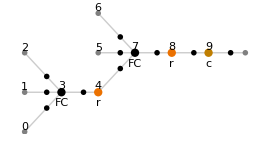
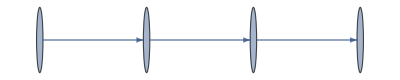
{NetChain[<>],0.,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{net=NetInitialize@NetChain[{30,Ramp,1,Ramp},"Input"->2,"Output"->NetDecoder["Scalar"]],net[{1,1}],NetInformation[net,"MXNetNodeGraphPlot"],NetInformation[net,"SummaryGraphic"],NetInformation[net,"LayersGraph"]}
```

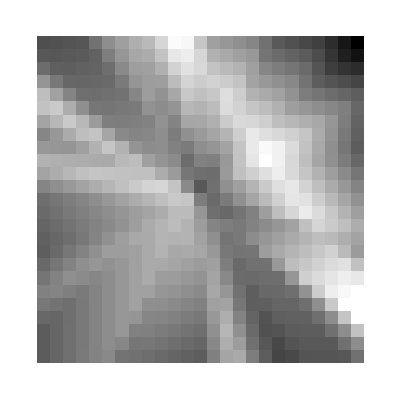
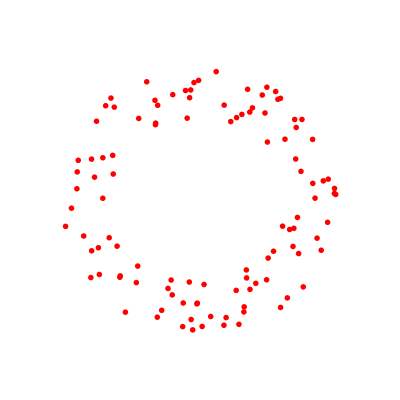

```mathematica
trained=NetTrain[net,data,MaxTrainingRounds->Quantity[10,"Seconds"],Method->{"SGD","LearningRate"->0.001},TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.1}];
f=trained;
o
```

```mathematica
f=NetTrain[net,data,MaxTrainingRounds->1000,Method->{"SGD","LearningRate"->0.01}]
```

NetChain[<>]

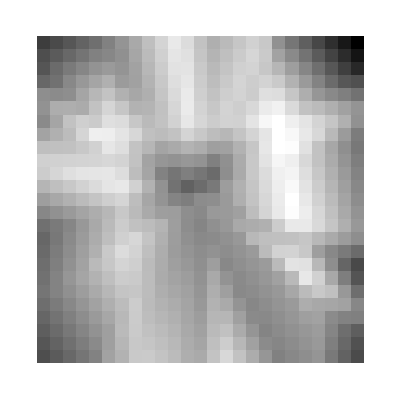
-Graphics--Graphics-

```mathematica
o
```

## plot

```mathematica
plotSolution[net_,t_]:=Overlay[{k[net],l,Style[t,Red,Bold,FontSize->24]}]
```

```mathematica
trained=NetTrain[net,data,MaxTrainingRounds->Quantity[10,"Seconds"],TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.1}];
```